```mathematica
GUASS[time_,delay_,sigma_]:=Exp[-0.5*((time-delay)/sigma)^2]
```

```mathematica
(*Mid infrared: 0.207 eV*)
```

```mathematica
tc=0.658;
500/tc
```

759.878

```mathematica
FWHM =100  (*fs*)
sigmafs =FWHM/2.355 (*fs*)
sigma = sigmafs/tc (*1/eV*)
```

100

42.4628

64.5332

```mathematica
FWHMp =200(*fs*)
sigmafsp =FWHMp/2.355 (*fs*)
sigmap = sigmafsp/tc (*1/eV*)
```

200

84.9257

129.066

```mathematica
t0 =250/tc
```

379.939

```mathematica
omega =0.207
```

0.207

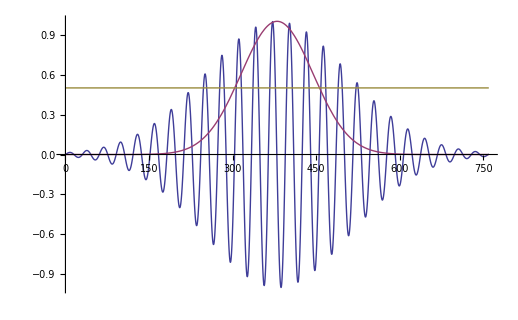

```mathematica
Plot[{GUASS[t,t0,sigmap]*Sin[omega*t],GUASS[t,t0,sigma],0.5},{t,0,500/tc}]
```

```mathematica
fac=207/3.84*1/10 (*->MC/cm*)
```

5.39063

```mathematica
{1,2,3,4,5}/fac
```

{0.185507,0.371014,0.556522,0.742029,0.927536}

```mathematica
tc=0.658;
800/tc
```

1215.81

```mathematica
FWHM =100  (*fs*)
sigmafs =FWHM/2.355 (*fs*)
sigma = sigmafs/tc (*1/eV*)
```

100

42.4628

64.5332

```mathematica
FWHMp =500(*fs*)
sigmafsp =FWHMp/2.355 (*fs*)
sigmap = sigmafsp/tc (*1/eV*)
```

500

212.314

322.666

```mathematica
t0 =530/tc
t1 = 350/tc
```

805.471

531.915

```mathematica
omega =0.004
```

0.004

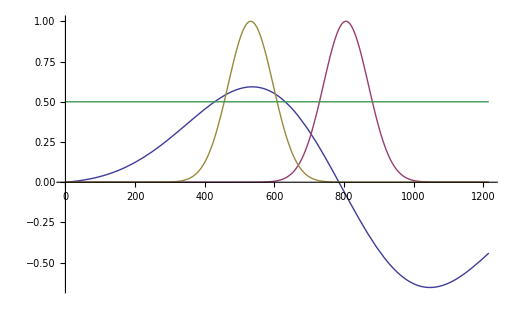

```mathematica
Plot[{GUASS[t,t0,sigmap]*Sin[omega*t],GUASS[t,t0,sigma],GUASS[t,t1,sigma],0.5},{t,0,800/tc}]
```

```mathematica
fac=4/3.84*1/10 (*->MC/cm*)
```

0.104167

```mathematica
{1}/fac
```

{9.6}

```mathematica
(*PRX*
```

```mathematica
tc=0.658;
150/tc
```

227.964

```mathematica
dur = 16.5/tc (*sigma = 16.5 fs*)
```

25.076

```mathematica
durpump =4/tc (*sigma = 4.0 fs*)
```

6.07903

```mathematica
t0 =75/tc
```

113.982

```mathematica
omega = 0.5
```

0.5

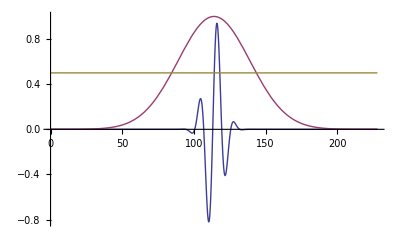

```mathematica
Plot[{GUASS[t,t0,durpump]*Sin[omega*t],GUASS[t,t0,dur],0.5},{t,0,150/tc}]
```

```mathematica
(*Linear Ramp*)
```

```mathematica
Al[t_]:=-EE*t
```

```mathematica
FullSimplify[Limit[Integrate[Al[t]/(t11-t22),{t,t11,t22}],t11->t11]]
FullSimplify[Limit[Integrate[Al[t]/(t11-t22),{t,t11,t22}],t11->t22]](*Shift is finite for t11==t22!!*)
```

1/2 EE (t11+t22)

EE t22

```mathematica
Integrate[Al[t]/epsilon,{t,t11,t11+epsilon}]
```

-(EE epsilon)/2-EE t11

```mathematica
Ag[t_,AA_,Omega_,Delay_,Sigma_]:=AA*Sin[Omega*t]*GUASS[t,Delay,Sigma]
```

```mathematica
NIntegrate[A[t,10.0,0.004,250.,65.]/(t11-t22),{t,t11,t22}]/.{t11->100.,t22->100.01}
```

NIntegrate::nlim: t = t11 is not a valid limit of integration.

-0.271712

```mathematica
NIntegrate[A[t,10.0,0.004,250.,65.]/(epsilon),{t,t11,t11+epsilon}]/.{t11->1.,epsilon->0.0000001}
```

NIntegrate::nlim: t = t11 is not a valid limit of integration.

0.0000260296

```mathematica
A[1.,10.0,0.004,250.,65.]
```

0.0000260296

```mathematica
GAUSS[time_,delay_,sigma_]:=1./(sigma*Sqrt[2.*Pi])Exp[-0.5*((time-delay)/sigma)^2]
```

```mathematica
t0=250.;
J0=0.2;
EE = 0.01;
BETA =100.0;
MU=0.4;
CUTOFF = 0.01;
f[w_,beta_]:=1./(Exp[w*beta]+1.)
epsilon[k_,J0_,EE_,t1_,t2_]:=-2.*J0*Cos[k-0.5*EE*(t1+t2)]
```

```mathematica
Photo[Omega_,k_,sigma_]:=Im[NIntegrate[GAUSS[t1,t0,sigma]*GAUSS[t2,t0,sigma]*I*f[epsilon[k,J0,EE,t1,t2]-MU,BETA]*Exp[I*(Omega+MU)*(t1-t2)-2.*I*epsilon[k,J0,EE,0.,0.]/EE*Sin[EE*(t1-t2)/2.]],{t1,0.,500.},{t2,0.,500.},Method->{"RiemannRule","Type"->"Right","Points"->100},MaxRecursion->0]]
```

```mathematica
Photo[0.0,Pi,15]
```

0.998143

```mathematica
Needs["PlotLegends`"]
```

LegendShadow::shdw: Symbol "LegendShadow" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
ListLinePlot[{Photo[Range[-1.0,-0.6,0.01],0.0,20],Photo[Range[-1.0,-0.6,0.01],0.0,30],Photo[Range[-1.0,-0.6,0.01],0.0,40],Photo[Range[-1.0,-0.6,0.01],0.0,50]},PlotRange->All,Frame->True,PlotStyle->{Thickness[0.005]},FrameLabel->{"FREQUENCY","IPHOTO"},PlotLegend->{"σ=20", "σ=30","σ=40","σ=50"},LegendPosition->{-0.7,0.1},LegendShadow->None]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t2 near {t1, t2} = {500., 500.}. NIntegrate obtained -2.95069×10^-19 + 4.06968×10^-11\ ⅈ and 1.13059×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t1 near {t1, t2} = {500., 500.}. NIntegrate obtained 2.06946×10^-19 + 2.34094×10^-10\ ⅈ and 2.82407×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in t2 near {t1, t2} = {500., 500.}. NIntegrate obtained -2.76497×10^-19 + 1.2863×10^-9\ ⅈ and 3.21872×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.